```mathematica
{InputField[Dynamic[x],String,FieldHint->"Enter a string"],Dynamic[x]}
```

{,}

```mathematica
str="Enter"
```

Enter

```mathematica
Dynamic[str]
```

```mathematica
whichCell[{x_,y_}]:={Ceiling[x/5],Ceiling[y/5]}
```

```mathematica
whichCell[{0,0}]
```

{1,1}

```mathematica
whichCell[{x_,y_}]:={IntegerPart[x/5]+1,IntegerPart[y/5]+1}
```

```mathematica
whichCell[{50,50}]
```

{11,11}

```mathematica
make3Lines[number_,length_]:=Flatten[{Table[Line[{{0,length/number i},{length,length/number i}}],{i,0,number}],Table[Line[{{length/number i,0},{length/number i,length}}],{i,0,number}]}]
```

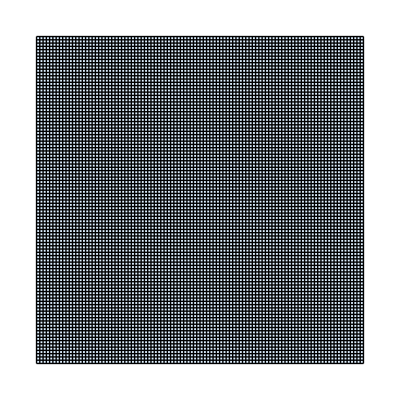

```mathematica
Graphics[{LightBlue,Rectangle[{0,0},{200,200}],Black,make3Lines[100,200]}]
```